```mathematica
rapp[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]/x2[[i,2]]},{i,1,Length[x1]}]
absrapp[x1_,x2_]:=Table[{x1[[i,1]],Abs[x1[[i,2]]/x2[[i,2]]]},{i,1,Length[x1]}]
mult[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]*x2[[i,2]]},{i,1,Length[x1]}]
sum[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]+x2[[i,2]]},{i,1,Length[x1]}]
sumlist[x1_]:=Table[{x1[[1,i,1]],x1[[1,i,2]]+x1[[2,i,2]]+x1[[3,i,2]]},{i,1,Length[x1[[1]]]}]
coeff[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]*c},{i,1,Length[x1]}]
sumconst[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]+c},{i,1,Length[x1]}]
diff[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]-x2[[i,2]]},{i,1,Length[x1]}]
joinbin[x_,n_]:=Map[{(Plus@@#)[[1]]/n,(Plus@@#)[[2]]}&,Partition[x,n]]
```

```mathematica
nomicartelle=Import["/Users/pagani/mg5_3.5/lista_cartellemumumassive.dat","List"]
quantities={aaWW,muaWW,mua,aa,mumu,total,nocutsmuaWW,OPmuaWW,OPmua,OPaa,OPmumu,OPtotal,OPnocutsmuaWW}
```

{aatottformuu,altottl,mupemtomupemtt,mupemtomupemtt_v0,mupemtomupemtt_v2,nocut_mupemtomupemtt,nocuts_altottl,onlyphoton_altottl,onlyphoton_mupemtomupemtt,onlyphoton_mupemtomupemtt_v0,onlyphoton_mupemtomupemtt_v2,onlyphoton_nocut_mupemtomupemtt,onlyphoton_nocuts_altottl}

{aaWW,muaWW,mua,aa,mumu,total,nocutsmuaWW,OPmuaWW,OPmua,OPaa,OPmumu,OPtotal,OPnocutsmuaWW}

-1

_m1

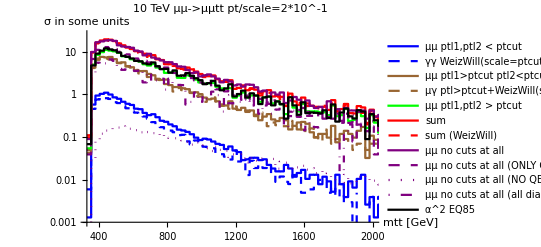

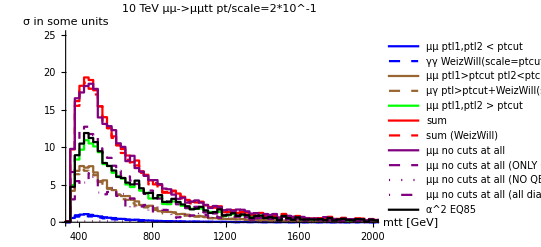

/Users/pagani/mu-vbf/massive_mu/plots/mttplots/logplotmtt10d0.pdf

/Users/pagani/mu-vbf/massive_mu/plots/mttplots/plotmtt10d0.pdf

```mathematica
namerun="distr2ndtry";
inputptcutscale=-1
ptcutscale=ToString[inputptcutscale];
ptcutscalev2=ToString[inputptcutscale];
If[inputptcutscale<0,ptcutscalev2="_m"<>ToString[Abs[inputptcutscale]]]


listaistogrammi=Table[0,{i,1,Length[nomicartelle]}];
Do[
nomi=.;
nhistos=.;
inputname="/Users/pagani/mg5_3.5/"<>nomicartelle[[i]]<>"/HTML/"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_scale_"<>ptcutscalev2<>"_energy_10000/MadAnalysis5job_0/Histograms/histos.saf";

If[i===6 || i===12,inputname="/Users/pagani/mg5_3.5/"<>nomicartelle[[i]]<>"/HTML/"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/tag_2_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_scale_"<>ptcutscalev2<>"_energy_10000/MadAnalysis5job_0/Histograms/histos.saf"];

If[ i===12,inputname="/Users/pagani/mg5_3.5/"<>nomicartelle[[i]]<>"/HTML/"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_scale_"<>ptcutscalev2<>"_energy_10000/MadAnalysis5job_0/Histograms/histos.saf"];


Estrai[inputname,quantities[[i]],nomi,nhistos],
{i,1,Length[nomicartelle]}];


Estrai["/Users/pagani/mg5_3.5/"<>"mupemtottbar_nophotons"<>"/HTML/"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_scale_"<>ptcutscalev2<>"_energy_10000/MadAnalysis5job_0/Histograms/histos.saf",NPtotal,nomiNP,nhistosNP]
nomiNP=.;
nhistosNP=.;

numberplot=11;

unisci[x_]:=joinbin[x,5];

summed=sum[mumu[numberplot],sum[aa[numberplot],mua[numberplot]]];
summedWWa=sum[mumu[numberplot],sum[aaWW[numberplot],muaWW[numberplot]]];
ZPtotal=diff[total[numberplot],sum[NPtotal[numberplot],OPtotal[numberplot]]];

RHS2nd82=diff[mua[numberplot], muaWW[numberplot]];
RHS3rd=diff[aa[numberplot], aaWW[numberplot]];
ddelta2S= diff[nocutsmuaWW[numberplot],coeff[aaWW[numberplot],2]];
RHS2nd83=diff[mua[numberplot], ddelta2S];
alpha2EQ85=sum[sum[mumu[numberplot],RHS2nd83],RHS3rd];


logplotmtt=ListLogPlot[{unisci[aa[numberplot]],unisci[aaWW[numberplot]],unisci[mua[numberplot]],unisci[ muaWW[numberplot]],unisci[mumu[numberplot]],unisci[summed],unisci[summedWWa],unisci[total[numberplot]],unisci[OPtotal[numberplot]],unisci[NPtotal[numberplot]],unisci[ZPtotal],unisci[alpha2EQ85]},Joined->True,InterpolationOrder->0,AxesLabel->{"mtt [GeV]","σ in some units"},LabelStyle->{FontSize->15},PlotRange->{{330,2000},{10^-3,25}},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all","μμ no cuts at all (ONLY QED)","μμ no cuts at all (NO QED)","μμ no cuts at all (all diag -(only QED + NO QED))","α^2 EQ85"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple,{Purple,Dashed},{Purple,Dotted},{Purple,DotDashed},Black},PlotLabel->"10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale]]

plotmtt=ListPlot[{unisci[aa[numberplot]],unisci[aaWW[numberplot]],unisci[mua[numberplot]],unisci[ muaWW[numberplot]],unisci[mumu[numberplot]],unisci[summed],unisci[summedWWa],unisci[total[numberplot]],unisci[OPtotal[numberplot]],unisci[NPtotal[numberplot]],unisci[ZPtotal],unisci[alpha2EQ85]},Joined->True,InterpolationOrder->0,AxesLabel->{"mtt [GeV]","σ in some units"},LabelStyle->{FontSize->15},PlotRange->{{330,2000},{10^-3,25}},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all","μμ no cuts at all (ONLY QED)","μμ no cuts at all (NO QED)","μμ no cuts at all (all diag -(only QED + NO QED))","α^2 EQ85"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple,{Purple,Dashed},{Purple,Dotted},{Purple,DotDashed},Black},PlotLabel->"10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale]]

Export["/Users/pagani/mu-vbf/massive_mu/plots/mttplots/logplotmtt10d"<>ToString[ptcutscale]<>".pdf",logplotmtt];
Export["/Users/pagani/mu-vbf/massive_mu/plots/mttplots/plotmtt10d"<>ToString[ptcutscale]<>".pdf",plotmtt];

"/Users/pagani/mu-vbf/massive_mu/plots/mttplots/logplotmtt10d0.pdf"
"/Users/pagani/mu-vbf/massive_mu/plots/mttplots/plotmtt10d0.pdf"
```

```mathematica
nomi
```

{{1_THT},{2_MET},{3_SQRTS},{4_PT},{5_ETA},{6_PT},{7_ETA},{8_PT},{9_ETA},{10_M},{11_M},{12_M},{13_M},{14_DELTAR},{15_DELTAR},{16_DELTAR}}

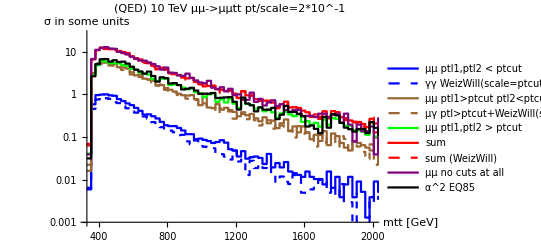

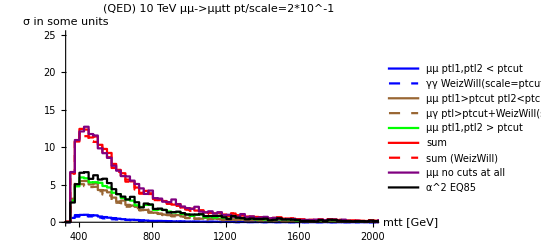

```mathematica
OPsummed=sum[OPmumu[numberplot],sum[OPaa[numberplot],OPmua[numberplot]]];
OPsummedWWa=sum[OPmumu[numberplot],sum[aaWW[numberplot],OPmuaWW[numberplot]]];

OPRHS2nd82=diff[OPmua[numberplot], OPmuaWW[numberplot]];
OPRHS3rd=diff[OPaa[numberplot], aaWW[numberplot]];
OPddelta2S= diff[OPnocutsmuaWW[numberplot],coeff[aaWW[numberplot],2]];
OPRHS2nd83=diff[OPmua[numberplot], OPddelta2S];
OPalpha2EQ85=sum[sum[OPmumu[numberplot],OPRHS2nd83],OPRHS3rd];

OPlogplotmtt=ListLogPlot[{unisci[OPaa[numberplot]],unisci[aaWW[numberplot]],unisci[OPmua[numberplot]],unisci[OPmuaWW[numberplot]],unisci[OPmumu[numberplot]],unisci[OPsummed],unisci[OPsummedWWa],unisci[OPtotal[numberplot]],unisci[OPalpha2EQ85]},Joined->True,InterpolationOrder->0,AxesLabel->{"mtt [GeV]","σ in some units"},LabelStyle->{FontSize->15},PlotRange->{{330,2000},{10^-3,25}},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all","α^2 EQ85"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple,Black},PlotLabel->"(QED) 10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale]]

OPplotmtt=ListPlot[{unisci[OPaa[numberplot]],unisci[aaWW[numberplot]],unisci[OPmua[numberplot]],unisci[OPmuaWW[numberplot]],unisci[OPmumu[numberplot]],unisci[OPsummed],unisci[OPsummedWWa],unisci[OPtotal[numberplot]],unisci[OPalpha2EQ85]},Joined->True,InterpolationOrder->0,AxesLabel->{"mtt [GeV]","σ in some units"},LabelStyle->{FontSize->15},PlotRange->{{330,2000},{10^-3,25}},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all","α^2 EQ85"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple,Black},PlotLabel->"(QED) 10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale]]
```

```mathematica
Export["/Users/pagani/mu-vbf/massive_mu/plots/mttplots/OPlogplotmtt10d"<>ToString[ptcutscale]<>".pdf",OPlogplotmtt];
Export["/Users/pagani/mu-vbf/massive_mu/plots/mttplots/OPplotmtt10d"<>ToString[ptcutscale]<>".pdf",OPplotmtt];
```

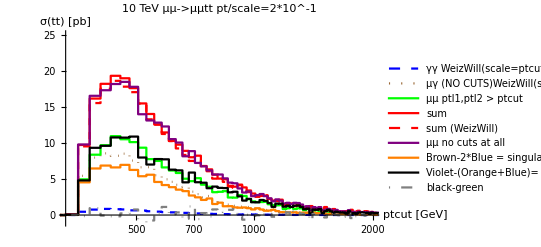

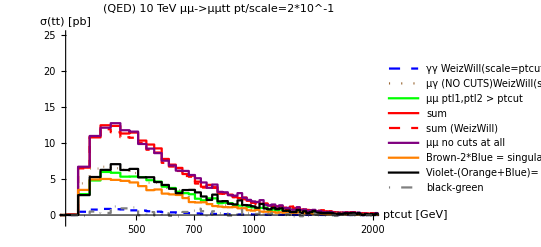

```mathematica
muaWWminus2aa=diff[nocutsmuaWW[numberplot],coeff[aaWW[numberplot],2]];
nodiv=diff[total[numberplot],sum[aaWW[numberplot],muaWWminus2aa]];
OPmuaWWminus2aa=diff[OPnocutsmuaWW[numberplot],coeff[aaWW[numberplot],2]];
OPnodiv=diff[OPtotal[numberplot],sum[aaWW[numberplot],OPmuaWWminus2aa]];


ListLogLinearPlot[{unisci[aaWW[numberplot]],unisci[nocutsmuaWW[numberplot]],unisci[mumu[numberplot]],unisci[summed],unisci[summedWWa],unisci[total[numberplot]],unisci[muaWWminus2aa],unisci[nodiv],unisci[diff[nodiv,mumu[numberplot]]]},Joined->True,InterpolationOrder->0,PlotLabel->"10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale],AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{ "γγ WeizWill(scale=ptcut)","μγ (NO CUTS)WeizWill(scale=ptcut)","μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all","Brown-2*Blue = singular div.", "Violet-(Orange+Blue)= μμ no cuts at all - (singular + double div.) ", "black-green"},PlotStyle->{{Blue,Dashed},{Brown,Dotted},Green,Red,{Red,Dashed},Purple,Orange,Black,{Gray,DotDashed}},PlotRange->{{330,2000},{-1,25}}]

ListLogLinearPlot[{unisci[aaWW[numberplot]],unisci[OPnocutsmuaWW[numberplot]],unisci[OPmumu[numberplot]],unisci[OPsummed],unisci[OPsummedWWa],unisci[OPtotal[numberplot]],unisci[OPmuaWWminus2aa],unisci[OPnodiv],unisci[diff[OPnodiv,OPmumu[numberplot]]]},Joined->True,InterpolationOrder->0,PlotLabel->"(QED) 10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale],AxesLabel->{"ptcut [GeV]","σ(tt) [pb]"},LabelStyle->{FontSize->15},PlotLegends->{ "γγ WeizWill(scale=ptcut)","μγ (NO CUTS)WeizWill(scale=ptcut)","μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all","Brown-2*Blue = singular div.", "Violet-(Orange+Blue)= μμ no cuts at all - (singular + double div.) ", "black-green"},PlotStyle->{{Blue,Dashed},{Brown,Dotted},Green,Red,{Red,Dashed},Purple,Orange,Black,{Gray,DotDashed}},PlotRange->{{330,2000},{-1,25}}]
```

```mathematica
(*namerun="distr2ndtry";
ptcutscale=ToString[2];


listaistogrammi=Table[0,{i,1,Length[nomicartelle]}];
Do[
nomi=.;
nhistos=.;
inputname="/Users/pagani/mg5_3.5/"<>nomicartelle[[i]]<>"/HTML/"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/tag_1_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/MadAnalysis5job_0/Histograms/histos.saf";

If[i===6 || i===12,inputname="/Users/pagani/mg5_3.5/"<>nomicartelle[[i]]<>"/HTML/"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/tag_2_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/MadAnalysis5job_0/Histograms/histos.saf"];

If[ i===12,inputname="/Users/pagani/mg5_3.5/"<>nomicartelle[[i]]<>"/HTML/"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/tag_3_MA5_PARTON_ANALYSIS_analysis1/Output/SAF/_"<>namerun<>"_scale_"<>ptcutscale<>"_energy_10000/MadAnalysis5job_0/Histograms/histos.saf"];


Estrai[inputname,quantities[[i]],nomi,nhistos],
{i,1,Length[nomicartelle]}]
numberplot=6;

unisci[x_]:=joinbin[x,5];

summed=sum[mumu[numberplot],sum[aa[numberplot],mua[numberplot]]];
summedWWa=sum[mumu[numberplot],sum[aaWW[numberplot],muaWW[numberplot]]];
logplotmtt=ListLogPlot[{unisci[aa[numberplot]],unisci[aaWW[numberplot]],unisci[mua[numberplot]],unisci[ muaWW[numberplot]],unisci[mumu[numberplot]],unisci[summed],unisci[summedWWa],unisci[total[numberplot]]},Joined->True,InterpolationOrder->0,AxesLabel->{"mtt [GeV]","σ in some units"},LabelStyle->{FontSize->15},PlotRange->{{0,1000},{10^-3,25}},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple},PlotLabel->"10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale]]

plotmtt=ListPlot[{unisci[aa[numberplot]],unisci[aaWW[numberplot]],unisci[mua[numberplot]],unisci[ muaWW[numberplot]],unisci[mumu[numberplot]],unisci[summed],unisci[summedWWa],unisci[total[numberplot]]},Joined->True,InterpolationOrder->0,AxesLabel->{"mtt [GeV]","σ in some units"},LabelStyle->{FontSize->15},PlotRange->{{0,1000},{10^-3,25}},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple},PlotLabel->"10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale]]


"/Users/pagani/mu-vbf/massive_mu/plots/mttplots/logplotmtt10d0.pdf"
"/Users/pagani/mu-vbf/massive_mu/plots/mttplots/plotmtt10d0.pdf"*)
```

```mathematica
(*OPsummed=sum[OPmumu[numberplot],sum[OPaa[numberplot],OPmua[numberplot]]];
OPsummedWWa=sum[OPmumu[numberplot],sum[aaWW[numberplot],OPmuaWW[numberplot]]];
OPlogplotmtt=ListLogPlot[{unisci[OPaa[numberplot]],unisci[aaWW[numberplot]],unisci[OPmua[numberplot]],unisci[OPmuaWW[numberplot]],unisci[OPmumu[numberplot]],unisci[OPsummed],unisci[OPsummedWWa],unisci[OPtotal[numberplot]]},Joined->True,InterpolationOrder->0,AxesLabel->{"mtt [GeV]","σ in some units"},LabelStyle->{FontSize->15},PlotRange->{{0,1000},{10^-3,25}},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple},PlotLabel->"(QED) 10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale]]

OPplotmtt=ListPlot[{unisci[OPaa[numberplot]],unisci[aaWW[numberplot]],unisci[OPmua[numberplot]],unisci[OPmuaWW[numberplot]],unisci[OPmumu[numberplot]],unisci[OPsummed],unisci[OPsummedWWa],unisci[OPtotal[numberplot]]},Joined->True,InterpolationOrder->0,AxesLabel->{"mtt [GeV]","σ in some units"},LabelStyle->{FontSize->15},PlotRange->{{0,1000},{10^-3,25}},PlotLegends->{"μμ ptl1,ptl2 < ptcut","γγ WeizWill(scale=ptcut)", "μμ ptl1>ptcut ptl2<ptcut", "μγ ptl>ptcut+WeizWill(scale=ptcut)", "μμ ptl1,ptl2 > ptcut", "sum","sum (WeizWill)","μμ no cuts at all"},PlotStyle->{Blue,{Blue,Dashed},Brown,{Brown,Dashed},Green,Red,{Red,Dashed},Purple},PlotLabel->"(QED) 10 TeV μμ->μμtt pt/scale=2*10^"<>ToString[ptcutscale]]*)
```

```mathematica
ZPtotal
```

{{-5.,0.},{0.,0.},{5.,0.},{10.,0.},{15.,0.},{20.,0.},{25.,0.},{30.,0.},{35.,0.},{40.,0.},{45.,0.},{50.,0.},{55.,0.},{60.,0.},{65.,0.},{70.,0.},{75.,0.},{80.,0.},{85.,0.},{90.,0.},{95.,0.},{100.,0.},{105.,0.},{110.,0.},{115.,0.},{120.,0.},{125.,0.},{130.,0.},{135.,0.},{140.,0.},{145.,0.},{150.,0.},{155.,0.},{160.,0.},{165.,0.},{170.,0.},{175.,0.},{180.,0.},{185.,0.},{190.,0.},{195.,0.},{200.,0.},{205.,0.},{210.,0.},{215.,0.},{220.,0.},{225.,0.},{230.,0.},{235.,0.},{240.,0.},{245.,0.},{250.,0.},{255.,0.},{260.,0.},{265.,0.},{270.,0.},{275.,0.},{280.,0.},{285.,0.},{290.,0.},{295.,0.},{300.,0.},{305.,0.},{310.,0.},{315.,0.},{320.,0.},{325.,0.},{330.,0.},{335.,0.},{340.,0.0497766},{345.,0.208765},{350.,0.409506},{355.,1.19981},{360.,0.791033},{365.,0.439667},{370.,0.630546},{375.,1.61334},{380.,1.09577},{385.,1.1549},{390.,0.982029},{395.,0.688587},{400.,0.890738},{405.,0.402162},{410.,1.52845},{415.,1.55959},{420.,0.912916},{425.,0.500437},{430.,1.24584},{435.,1.16063},{440.,1.46678},{445.,1.40909},{450.,1.83849},{455.,1.24249},{460.,0.857608},{465.,1.20165},{470.,0.921265},{475.,1.67463},{480.,1.27216},{485.,1.35784},{490.,0.821517},{495.,0.736204},{500.,0.854734},{505.,0.61801},{510.,0.914956},{515.,0.828575},{520.,0.735971},{525.,0.777832},{530.,0.0789959},{535.,1.31041},{540.,0.821642},{545.,1.14884},{550.,1.44622},{555.,0.197383},{560.,1.03986},{565.,0.212824},{570.,0.481744},{575.,1.25943},{580.,1.3011},{585.,0.927475},{590.,0.614661},{595.,0.182609},{600.,0.501},{605.,1.26777},{610.,0.916914},{615.,0.636145},{620.,0.690208},{625.,1.10971},{630.,0.816971},{635.,0.581609},{640.,0.56625},{645.,0.477571},{650.,-0.0953462},{655.,0.31971},{660.,0.472194},{665.,0.719567},{670.,0.926153},{675.,0.339356},{680.,1.03113},{685.,0.666316},{690.,0.214968},{695.,0.587695},{700.,0.212905},{705.,0.271882},{710.,0.323138},{715.,0.603328},{720.,0.581151},{725.,0.26927},{730.,0.345207},{735.,0.49629},{740.,0.413182},{745.,0.285211},{750.,0.578808},{755.,0.856661},{760.,0.104152},{765.,0.478631},{770.,0.319166},{775.,0.410416},{780.,0.187721},{785.,0.32299},{790.,0.0428779},{795.,0.49294},{800.,0.528487},{805.,0.352537},{810.,0.544036},{815.,0.391199},{820.,0.909477},{825.,0.770554},{830.,-0.170577},{835.,0.294411},{840.,0.0311861},{845.,0.697938},{850.,0.0852082},{855.,0.459414},{860.,0.254971},{865.,0.153229},{870.,0.340216},{875.,0.626989},{880.,0.328016},{885.,0.126916},{890.,0.206441},{895.,0.238286},{900.,-0.221171},{905.,-0.0297451},{910.,0.297216},{915.,0.287868},{920.,0.0917216},{925.,0.271845},{930.,0.0530138},{935.,0.197079},{940.,0.046619},{945.,0.344695},{950.,0.226983},{955.,0.230645},{960.,-0.0042486},{965.,0.29477},{970.,-0.0542197},{975.,0.349649},{980.,0.300341},{985.,0.259919},{990.,-0.192052},{995.,0.140018},{1000.,0.0658757},{1005.,0.258673},{1010.,0.0547673},{1015.,0.393499},{1020.,-0.0617055},{1025.,0.253056},{1030.,0.137674},{1035.,0.274455},{1040.,0.19112},{1045.,0.269353},{1050.,0.429442},{1055.,-0.0518432},{1060.,-0.0486491},{1065.,0.548874},{1070.,0.273404},{1075.,0.152685},{1080.,0.229165},{1085.,0.13452},{1090.,0.165086},{1095.,0.25185},{1100.,-0.124694},{1105.,0.161223},{1110.,-0.0413578},{1115.,0.145394},{1120.,0.310203},{1125.,0.159314},{1130.,0.0654867},{1135.,0.184102},{1140.,0.23497},{1145.,0.075115},{1150.,-0.0313011},{1155.,0.28646},{1160.,0.0781146},{1165.,0.205696},{1170.,0.261089},{1175.,0.291803},{1180.,0.0187097},{1185.,0.223238},{1190.,-0.183007},{1195.,0.115108},{1200.,0.076206},{1205.,0.123646},{1210.,0.203982},{1215.,0.143097},{1220.,0.0858344},{1225.,0.300186},{1230.,0.155725},{1235.,0.0663832},{1240.,0.135845},{1245.,0.184141},{1250.,0.147382},{1255.,0.0272865},{1260.,0.197392},{1265.,0.372842},{1270.,0.281786},{1275.,0.107622},{1280.,0.185427},{1285.,-0.0216727},{1290.,-0.0107984},{1295.,0.107622},{1300.,0.249747},{1305.,-0.0607299},{1310.,0.155296},{1315.,0.314294},{1320.,0.0206643},{1325.,0.0760115},{1330.,0.117445},{1335.,0.0497371},{1340.,0.0852114},{1345.,0.223044},{1350.,0.0356292},{1355.,0.0666172},{1360.,0.213221},{1365.,0.105091},{1370.,-0.160128},{1375.,-0.162465},{1380.,0.124542},{1385.,0.0841598},{1390.,0.0382002},{1395.,0.0388232},{1400.,-0.0122389},{1405.,0.0653317},{1410.,0.163639},{1415.,0.09332},{1420.,0.157244},{1425.,0.234581},{1430.,0.0469715},{1435.,-0.0611585},{1440.,0.0593655},{1445.,0.0452575},{1450.,0.271769},{1455.,0.154673},{1460.,-0.0118104},{1465.,0.029429},{1470.,0.11729},{1475.,0.0181261},{1480.,0.0151266},{1485.,-0.0421359},{1490.,0.0625661},{1495.,0.115148},{1500.,-0.0519587},{1505.,0.118342},{1510.,-0.0113424},{1515.,0.136936},{1520.,0.184376},{1525.,0.0166461},{1530.,0.156816},{1535.,-0.062444},{1540.,0.117913},{1545.,-0.0107193},{1550.,0.12797},{1555.,-0.064158},{1560.,0.165158},{1565.,0.0771025},{1570.,0.0756225},{1575.,0.0762455},{1580.,0.0247549},{1585.,0.00830328},{1590.,-0.0419018},{1595.,0.0463485},{1600.,0.146564},{1605.,0.0681367},{1610.,0.0574569},{1615.,0.0659941},{1620.,0.0288059},{1625.,0.00616074},{1630.,-0.00237656},{1635.,0.155336},{1640.,0.0170746},{1645.,0.00873179},{1650.,-0.000662518},{1655.,0.0384343},{1660.,0.0578854},{1665.,0.0649427},{1670.,0.00873179},{1675.,0.0672797},{1680.,0.136741},{1685.,-0.0904324},{1690.,0.0179316},{1695.,-0.120563},{1700.,-0.0532442},{1705.,0.0764795},{1710.,-0.0188281},{1715.,0.0170746},{1720.,0.0275204},{1725.,0.0884449},{1730.,0.0670852},{1735.,0.136313},{1740.,0.0578854},{1745.,-0.0878613},{1750.,0.00853729},{1755.,0.00725176},{1760.,0.000817572},{1765.,-0.00237656},{1770.,0.0192171},{1775.,0.117953},{1780.,-0.000662518},{1785.,0.0589369},{1790.,-0.107741},{1795.,-0.00109103},{1800.,-0.000662518},{1805.,0.00768027},{1810.,0.0589764},{1815.,-0.0498161},{1820.,-0.0502446},{1825.,-0.00175348},{1830.,0.106377},{1835.,-0.0207367},{1840.,0.0786221},{1845.,-0.031222},{1850.,0.176501},{1855.,-0.0299365},{1860.,0.0683707},{1865.,0.0294685},{1870.,-0.0228792},{1875.,0.0777651},{1880.,0.118381},{1885.,0.0589764},{1890.,0.0972162},{1895.,0.0480626},{1900.,0.0192171},{1905.,0.0670852},{1910.,-0.0134849},{1915.,0.059171},{1920.,0.0373827},{1925.,0.0781936},{1930.,0.0583139},{1935.,-0.00214255},{1940.,0.0955022},{1945.,0.0166461},{1950.,0.0378112},{1955.,0.0576909},{1960.,0.0476341},{1965.,-0.0397593},{1970.,0.127776},{1975.,0.0100173},{1980.,0.0373827},{1985.,0.0683707},{1990.,-0.0117709},{1995.,0.0882504},{2000.,0.0382398},{2005.,0.0683707},{2010.,0.0271314},{2015.,0.0267029},{2020.,-0.0113424},{2025.,0.0683707},{2030.,-0.0493876},{2035.,0.0583139},{2040.,-0.0192566},{2045.,0.0985017},{2050.,0.00853729},{2055.,0.0687992},{2060.,-0.000662518},{2065.,-0.0109138},{2070.,0.0576909},{2075.,0.0267029},{2080.,0.0555483},{2085.,0.0786221},{2090.,-0.000857019},{2095.,0.0679422},{2100.,0.0687992},{2105.,-0.0493876},{2110.,0.0279884},{2115.,-0.0299365},{2120.,-0.0397593},{2125.,0.0279884},{2130.,-0.029508},{2135.,0.0878219},{2140.,0.0581194},{2145.,0.000194501},{2150.,0.117096},{2155.,-0.0104853},{2160.,0.117524},{2165.,0.0878219},{2170.,-0.00299957},{2175.,0.00768027},{2180.,-0.0600674},{2185.,0.00853729},{2190.,0.00939431},{2195.,-0.0220222},{2200.,-0.00128553},{2205.,0.0089658},{2210.,0.0386683},{2215.,-0.0211652},{2220.,0.0378112},{2225.,0.0878219},{2230.,0.0581194},{2235.,-0.030365},{2240.,0.00768027},{2245.,0.000623011},{2250.,0.0390968},{2255.,-0.0211652},{2260.,-0.0485306},{2265.,0.0288455},{2270.,0.0200741},{2275.,0.0373827},{2280.,0.00810878},{2285.,-0.0493876},{2290.,0.029274},{2295.,-0.0224507},{2300.,0.00982282},{2305.,-0.0290794},{2310.,0.0594049},{2315.,-0.0393308},{2320.,0.0390968},{2325.,0.0878219},{2330.,0.00982282},{2335.,-0.00171404},{2340.,0.0395253},{2345.,0.0382398},{2350.,-0.0211652},{2355.,0.0382398},{2360.,-0.060496},{2365.,-0.00171404},{2370.,-0.0104853},{2375.,-0.029508},{2380.,0.0288455},{2385.,0.029274},{2390.,0.0576909},{2395.,0.0585479},{2400.,-0.00962832},{2405.,-0.0207367},{2410.,0.0395253},{2415.,0.0589764},{2420.,-0.0207367},{2425.,0.0585479},{2430.,-0.0100568},{2435.,-0.0203082},{2440.,0.0288455},{2445.,0.00982282},{2450.,0.000623011},{2455.,0.0288455},{2460.,-0.000857019},{2465.,-0.0397593},{2470.,0.00768027},{2475.,0.00939431},{2480.,-0.000428509},{2485.,0.00982282},{2490.,-0.0397593},{2495.,0.0196456},{2500.,0.0886789},{2505.,-0.000428509},{2510.,-0.0393308},{2515.,0.0284169},{2520.,-0.000857019},{2525.,-0.000857019},{2530.,-0.00128553},{2535.,-0.0104853},{2540.,-0.0207367},{2545.,0.00982282},{2550.,-0.0401878},{2555.,-0.00128553},{2560.,-0.0299365},{2565.,-0.030365},{2570.,0.0687992},{2575.,0.0581194},{2580.,-0.0203082},{2585.,-0.0203082},{2590.,0.030754},{2595.,0.0279884},{2600.,0.0288455},{2605.,-0.000428509},{2610.,0.0284169},{2615.,0.00853729},{2620.,0.0589764},{2625.,-0.00128553},{2630.,-0.00128553},{2635.,-0.00214255},{2640.,0.00982282},{2645.,-0.0203082},{2650.,-0.0203082},{2655.,0.0585479},{2660.,-0.000857019},{2665.,0.0288455},{2670.,0.0696563},{2675.,0.00982282},{2680.,-0.0207367},{2685.,-0.00962832},{2690.,-0.0194511},{2695.,-0.0393308},{2700.,0.00939431},{2705.,-0.0194511},{2710.,0.0279884},{2715.,0.00939431},{2720.,0.0576909},{2725.,-0.00128553},{2730.,0.029274},{2735.,-0.0198796},{2740.,-0.000428509},{2745.,-0.0397593},{2750.,-0.00128553},{2755.,0.0594049},{2760.,-0.0194511},{2765.,0.0585479},{2770.,0.118381},{2775.,0.0297025},{2780.,0.0288455},{2785.,0.},{2790.,0.029274},{2795.,-0.0397593},{2800.,0.0279884},{2805.,-0.00171404},{2810.,-0.000857019},{2815.,0.0585479},{2820.,-0.00128553},{2825.,-0.000428509},{2830.,-0.000428509},{2835.,0.},{2840.,0.},{2845.,0.},{2850.,-0.00128553},{2855.,-0.0198796},{2860.,0.},{2865.,0.0089658},{2870.,0.00939431},{2875.,-0.000428509},{2880.,-0.000857019},{2885.,0.0297025},{2890.,-0.000428509},{2895.,-0.0194511},{2900.,-0.0389023},{2905.,0.},{2910.,-0.000428509},{2915.,-0.000857019},{2920.,0.0297025},{2925.,-0.0207367},{2930.,-0.0198796},{2935.,-0.000428509},{2940.,0.},{2945.,-0.0207367},{2950.,-0.0393308},{2955.,-0.00128553},{2960.,-0.000857019},{2965.,-0.0397593},{2970.,-0.0198796},{2975.,-0.0194511},{2980.,0.0589764},{2985.,0.},{2990.,0.029274},{2995.,-0.0393308},{3000.,0.0390968},{3005.,-0.00171404},{3010.,-0.0194511},{3015.,-0.000428509},{3020.,-0.000428509},{3025.,0.},{3030.,0.0297025},{3035.,-0.0393308},{3040.,-0.00128553},{3045.,-0.0198796},{3050.,0.},{3055.,-0.0198796},{3060.,0.0288455},{3065.,0.0284169},{3070.,0.0102513},{3075.,0.0288455},{3080.,-0.000428509},{3085.,0.029274},{3090.,0.0297025},{3095.,0.0102513},{3100.,0.0288455},{3105.,0.0297025},{3110.,0.0288455},{3115.,-0.000428509},{3120.,-0.000428509},{3125.,-0.000428509},{3130.,0.029274},{3135.,0.0102513},{3140.,-0.000857019},{3145.,0.},{3150.,0.0594049},{3155.,-0.000428509},{3160.,-0.0194511},{3165.,-0.000428509},{3170.,0.},{3175.,-0.0198796},{3180.,0.0594049},{3185.,0.0297025},{3190.,0.00939431},{3195.,-0.000428509},{3200.,-0.0203082},{3205.,0.0891074},{3210.,-0.000428509},{3215.,-0.000428509},{3220.,0.0297025},{3225.,0.0102513},{3230.,0.0594049},{3235.,-0.0203082},{3240.,-0.0194511},{3245.,0.},{3250.,-0.000428509},{3255.,-0.0100568},{3260.,0.},{3265.,0.0589764},{3270.,-0.00128553},{3275.,0.},{3280.,-0.000857019},{3285.,-0.0203082},{3290.,-0.000428509},{3295.,0.0297025},{3300.,0.0589764},{3305.,-0.000857019},{3310.,0.},{3315.,-0.000428509},{3320.,0.0297025},{3325.,-0.000428509},{3330.,-0.000428509},{3335.,-0.000428509},{3340.,0.029274},{3345.,-0.0198796},{3350.,0.0589764},{3355.,0.0594049},{3360.,-0.0203082},{3365.,0.},{3370.,-0.0194511},{3375.,-0.000428509},{3380.,0.},{3385.,-0.000428509},{3390.,-0.000428509},{3395.,0.},{3400.,0.0297025},{3405.,-0.000428509},{3410.,0.},{3415.,0.},{3420.,0.},{3425.,-0.00962832},{3430.,0.},{3435.,0.},{3440.,-0.000428509},{3445.,0.0297025},{3450.,-0.000428509},{3455.,0.},{3460.,0.},{3465.,0.029274},{3470.,0.},{3475.,0.0297025},{3480.,-0.00128553},{3485.,0.},{3490.,0.0288455},{3495.,0.},{3500.,-0.0194511},{3505.,-0.000428509},{3510.,-0.000428509},{3515.,-0.000428509},{3520.,-0.0194511},{3525.,0.},{3530.,0.029274},{3535.,0.},{3540.,-0.000428509},{3545.,0.},{3550.,0.0297025},{3555.,0.},{3560.,-0.0194511},{3565.,0.},{3570.,0.},{3575.,-0.000857019},{3580.,0.},{3585.,0.0594049},{3590.,0.},{3595.,0.},{3600.,0.0297025},{3605.,-0.000428509},{3610.,0.},{3615.,0.0102513},{3620.,0.029274},{3625.,-0.0389023},{3630.,-0.0397593},{3635.,-0.000857019},{3640.,0.0297025},{3645.,-0.000428509},{3650.,0.},{3655.,0.},{3660.,-0.000428509},{3665.,-0.000428509},{3670.,0.},{3675.,-0.000428509},{3680.,0.},{3685.,0.},{3690.,0.},{3695.,0.},{3700.,0.0297025},{3705.,0.},{3710.,0.},{3715.,-0.000857019},{3720.,-0.000428509},{3725.,0.},{3730.,0.029274},{3735.,-0.0194511},{3740.,-0.000428509},{3745.,0.},{3750.,0.},{3755.,-0.0194511},{3760.,0.},{3765.,0.029274},{3770.,0.},{3775.,0.},{3780.,0.0594049},{3785.,0.},{3790.,0.},{3795.,0.0297025},{3800.,0.},{3805.,0.},{3810.,0.},{3815.,-0.000428509},{3820.,-0.000428509},{3825.,-0.000857019},{3830.,-0.000428509},{3835.,0.},{3840.,0.},{3845.,0.},{3850.,0.0297025},{3855.,0.},{3860.,-0.000428509},{3865.,-0.0194511},{3870.,0.},{3875.,-0.000428509},{3880.,-0.0194511},{3885.,0.},{3890.,0.},{3895.,0.0297025},{3900.,-0.000428509},{3905.,0.},{3910.,0.},{3915.,0.},{3920.,-0.000428509},{3925.,0.},{3930.,-0.0194511},{3935.,0.},{3940.,0.},{3945.,0.0102513},{3950.,-0.000428509},{3955.,0.0288455},{3960.,0.},{3965.,0.},{3970.,0.},{3975.,0.},{3980.,0.},{3985.,0.},{3990.,0.0297025},{3995.,0.029274},{4000.,0.0297025},{4005.,-0.000428509},{4010.,-0.000857019},{4015.,0.029274},{4020.,-0.000428509},{4025.,0.},{4030.,0.0297025},{4035.,-0.000428509},{4040.,-0.0198796},{4045.,0.},{4050.,-0.000857019},{4055.,-0.0198796},{4060.,0.},{4065.,0.},{4070.,0.},{4075.,-0.0194511},{4080.,0.},{4085.,0.},{4090.,0.},{4095.,0.},{4100.,-0.0194511},{4105.,0.},{4110.,0.},{4115.,0.},{4120.,0.},{4125.,-0.0194511},{4130.,0.},{4135.,0.},{4140.,0.},{4145.,-0.000428509},{4150.,0.},{4155.,0.},{4160.,-0.000857019},{4165.,0.},{4170.,0.},{4175.,0.},{4180.,0.},{4185.,0.},{4190.,0.},{4195.,0.},{4200.,-0.000428509},{4205.,0.},{4210.,-0.000428509},{4215.,0.},{4220.,0.},{4225.,0.0297025},{4230.,0.},{4235.,-0.0194511},{4240.,0.0297025},{4245.,0.},{4250.,0.},{4255.,0.},{4260.,0.},{4265.,-0.000428509},{4270.,0.},{4275.,0.},{4280.,-0.0194511},{4285.,0.},{4290.,0.},{4295.,0.0297025},{4300.,0.},{4305.,0.},{4310.,0.},{4315.,0.},{4320.,0.},{4325.,0.},{4330.,-0.000428509},{4335.,0.},{4340.,0.},{4345.,0.},{4350.,0.},{4355.,0.},{4360.,0.},{4365.,-0.00128553},{4370.,0.},{4375.,0.},{4380.,0.},{4385.,0.},{4390.,0.0297025},{4395.,0.},{4400.,0.0102513},{4405.,0.},{4410.,0.},{4415.,-0.000428509},{4420.,0.},{4425.,0.},{4430.,0.},{4435.,0.0297025},{4440.,0.},{4445.,0.},{4450.,0.},{4455.,0.},{4460.,0.},{4465.,0.},{4470.,0.},{4475.,0.},{4480.,0.},{4485.,0.},{4490.,0.},{4495.,0.},{4500.,0.},{4505.,-0.000857019},{4510.,0.0297025},{4515.,0.},{4520.,0.},{4525.,0.},{4530.,0.0297025},{4535.,0.},{4540.,0.},{4545.,0.},{4550.,-0.000428509},{4555.,-0.000428509},{4560.,0.},{4565.,0.},{4570.,0.},{4575.,0.},{4580.,0.0297025},{4585.,-0.0194511},{4590.,-0.000428509},{4595.,0.},{4600.,0.},{4605.,0.},{4610.,-0.000428509},{4615.,0.},{4620.,0.},{4625.,0.},{4630.,0.},{4635.,0.},{4640.,0.},{4645.,0.},{4650.,0.},{4655.,0.},{4660.,0.},{4665.,0.},{4670.,0.0297025},{4675.,0.},{4680.,-0.000428509},{4685.,0.},{4690.,0.},{4695.,-0.000428509},{4700.,-0.0194511},{4705.,0.},{4710.,0.},{4715.,0.},{4720.,0.},{4725.,0.},{4730.,0.},{4735.,0.},{4740.,0.},{4745.,-0.000428509},{4750.,0.},{4755.,-0.000428509},{4760.,-0.000428509},{4765.,0.},{4770.,0.},{4775.,0.},{4780.,0.},{4785.,0.},{4790.,0.},{4795.,0.},{4800.,0.},{4805.,0.},{4810.,0.},{4815.,0.},{4820.,0.},{4825.,0.},{4830.,0.},{4835.,-0.0194511},{4840.,0.},{4845.,-0.000428509},{4850.,0.},{4855.,0.},{4860.,0.},{4865.,0.},{4870.,0.},{4875.,0.},{4880.,0.},{4885.,0.},{4890.,-0.000428509},{4895.,0.},{4900.,-0.000428509},{4905.,0.},{4910.,0.0297025},{4915.,0.},{4920.,0.},{4925.,-0.000428509},{4930.,0.},{4935.,0.},{4940.,0.},{4945.,0.},{4950.,-0.000428509},{4955.,0.},{4960.,0.},{4965.,0.},{4970.,0.0288455},{4975.,0.},{4980.,0.},{4985.,0.},{4990.,0.},{4995.,0.},{5000.,0.0928915}}